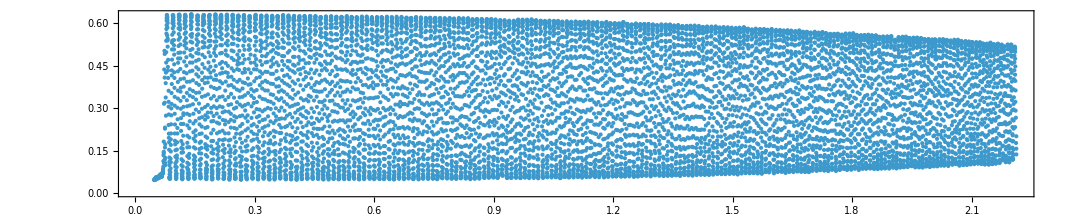

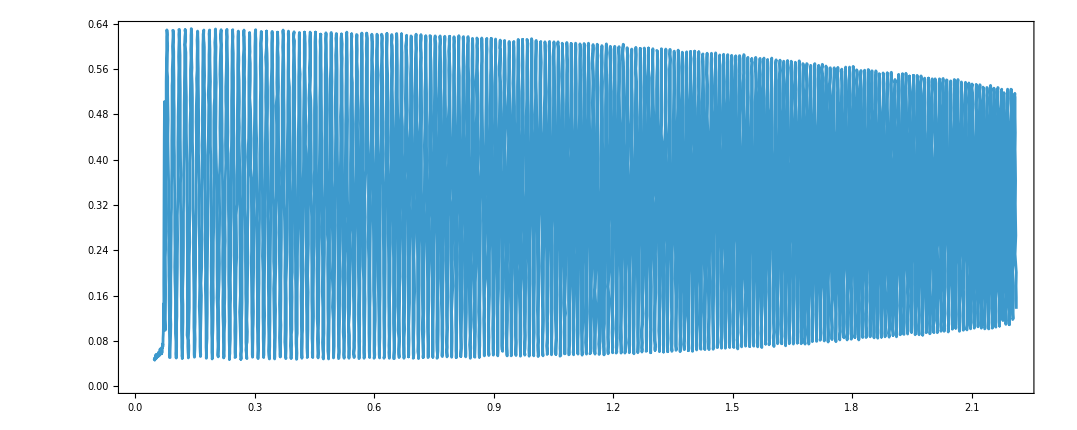

```mathematica
"Importa i dati da analizzare";SetDirectory["/home/tom/Onedrive/Documenti/Scuola/Uni/2 anno/Ottica/Relazioni/Gruppo19"];file=ToExpression[Drop[Import["laser-verde1.csv","Data"],3]];
file=Select[file,#1[[3]]<2.5&];
file=Select[file,0<#1[[2]]<5.0&];
bin=2;file1=Total[Partition[file,bin],{2}]/bin;sine=Transpose[{file1[[All,2]],file1[[All,3]]}];
sine=Transpose[{file[[All,2]],file[[All,3]]}];ListPlot[sine,Joined->False,Frame->True,Axes->False,PlotRange->All,AspectRatio->0.2] 
ListPlot[sine[[1;;Length[sine]]],Joined->True,Frame->True,Axes->False,PlotRange->All,AspectRatio->0.4]
sin = sine[[All, 2]];
volt=sine[[All,1]];dim=Dimensions[sin][[1]];
```

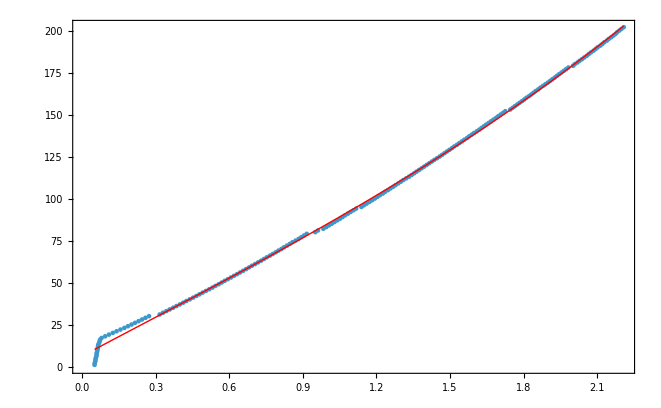

{a→6.26822,b→77.2754,c→-1.86899,d→3.24189}

{0.445067,1.84428,1.97422,0.587971}

634.854

```mathematica
"Elenca i massimi";
list={};s=2;n=0;d=.;
Do[If[sin[[i]]-sin[[i-s]]>0,If[sin[[i+s]]-sin[[i]]<0,n=n+1;list=Append[list,{volt[[i]],n}]]],{i,s,dim-s,s}]
g=ListPlot[list,Frame->True,Axes->False,PlotRange->All,PlotStyle->{PointSize[0.005]}];
"stima del periodo";per=list[[2,1]]-list[[1,1]];
"fit della lista di massimi con un polinomio di terzo grado";
fit=NonlinearModelFit[ list,a+b x+c x^2+d x^3,{{a,0.5},{b,10},{c,0.1},{d,1}},x];
gg=Plot[fit["BestFit"],{x,list[[All,1]][[1]],list[[All,1]][[-1]]},PlotStyle->{Red,Thin},PlotRange->All];
graph=Show[g,gg]
fit["BestFitParameters"]
fit["ParameterErrors"]
Total[fit["FitResiduals"]^2]
```

```mathematica
list
```

```mathematica
"Procedura di confronto degli andamenti per le sorgenti He-Ne e semiconduttore nel verde. "
fileverde=ToExpression[Drop[Import["laser-verde4.csv","Data"],3]];
filerosso=ToExpression[Drop[Import["laser-rosso4.csv","Data"] ,3]]; "laser He-Ne";
file=Select[fileverde,0<#[[2]]<2.5&];
bin=2;
file1=Total[Partition[file,bin],{2}]/bin;
sine=Transpose[{file1[[All,2]],file1[[All,3]]}];
sin=sine[[All,2]];volt=sine[[All,1]];dim=Dimensions[sin][[1]];
listv={};s=5;n=0;d=.;
Do[If[sin[[i]]-sin[[i-s]]>0,If[sin[[i+s]]-sin[[i]]<0,n=n+1;listv=Append[listv,{volt[[i]],n}]]],{i,s,dim-s,s}]
file=Select[filerosso,#[[3]]<2.5&];
bin=2;
file1=Total[Partition[file,bin],{2}]/bin;
sine=Transpose[{file1[[All,2]],file1[[All,3]]}];
sin=sine[[All,2]];volt=sine[[All,1]];dim=Dimensions[sin][[1]];
listr={};s=5;n=0;d=.;
Do[If[sin[[i]]-sin[[i-s]]>0,If[sin[[i+s]]-sin[[i]]<0,n=n+1;listr=Append[listr,{volt[[i]],n}]]],{i,s,dim-s,s}]
Manipulate[g=ListPlot[listr,Frame->True,Axes->False,PlotRange->All,Joined->True, PlotStyle->{Red,Thickness[0.001]}];
gg=ListPlot[Transpose[{listv[[All,1]],factor(listv[[All,2]]-off)} ],Joined->True,Frame->True,Axes->False,PlotRange->All,PlotStyle->{Green,Thickness[0.001]}];Show[g,gg,ImageSize->{800},Epilog->Inset[factor,{Center,Center}]],{{factor,1.0001,"F"},0.5,1.5},{{off,0,"offset"},-200,200}]
```

Procedura di confronto degli andamenti per le sorgenti He-Ne e semiconduttore nel verde.

```mathematica
"Procedura di confronto degli andamenti per le sorgenti He-Ne e semiconduttore nel verde. "
```

Procedura di confronto degli andamenti per le sorgenti He-Ne e semiconduttore nel verde.

```mathematica
"Analisi lunghezza di coerenza";
file=ToExpression[Drop[Import["laser-verde1.csv","Data"],3]]; 
(*file=Select[file,0<#1[[2]]<2.5&];
file=Select[file,#1[[2]]<2.5&];
file=Select[file,0<#1[[2]]<5.0&];*)
bin=2;
file1=Total[Partition[file,bin],{2}]/bin;
sine=Transpose[{file1[[All,2]],file1[[All,3]]}];
sine=sine[[340;;2500]];
Manipulate[lc=ListPlot[sine[[1;;Length[sine]]],Joined->True,Frame->True,Axes->False,PlotRange->All,AspectRatio->0.4];l1=Plot[up,{x,sine[[1,1]],sine[[-1,1]]},Frame->True,Axes->False,PlotRange->All, PlotStyle->{Red,Thickness[0.001]}];
l2=Plot[down,{x,sine[[1,1]],sine[[-1,1]]},Frame->True,Axes->False,PlotRange->All, PlotStyle->{Green,Thickness[0.001]}];
Show[lc,l1,l2,ImageSize->{800},Epilog->{Inset[up,{Center,up}],Inset[down,{Center,down}]}],{{up,Max[sine[[All,2]]],"up"},0.9Min[sine[[All,2]]],1.1Max[sine[[All,2]]]},{{down,Min[sine[[All,2]]],"down"},0.9Min[sine[[All,2]]],1.1Max[sine[[All,2]]]}]
```

```mathematica
x
```

```mathematica
§
```

```mathematica
Dimensions[sine]
```

{726,2}